## Data Visualization

### Data Visualization

```mathematica
1
```

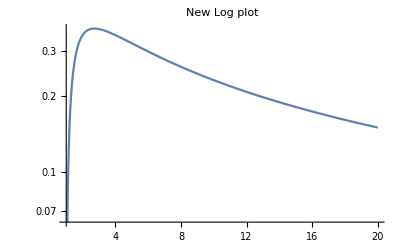

```mathematica
LogPlot[Log[x]/x,{x,1,20},PlotLabel->"New Log plot"]
```

```mathematica
2
```

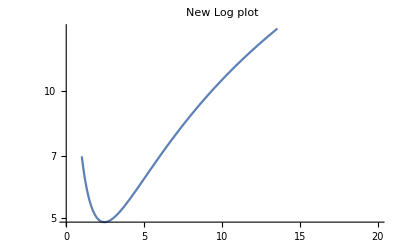

```mathematica
LogPlot[x+6/x,{x,1,20},PlotLabel->"New Log plot",PlotRange->{0,14}]
```

```mathematica
3
```

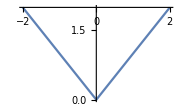

```mathematica
Plot[Abs[x],{x,-2,2},AxesOrigin->{0,2}]
```

```mathematica
4
```

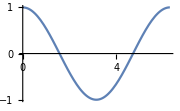
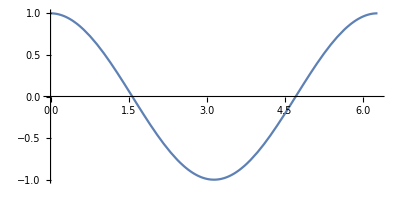

```mathematica
{Plot[Cos[x],{x,0,2π},ImageSize->Small], Plot[Cos[x],{x,0,2π},AspectRatio->1/2]}
```

### Plotting Data

```mathematica
5
```

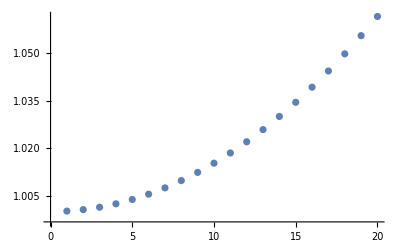

```mathematica
ListPlot[Table[Cosh[i Degree],{i,1,20}]]
```

```mathematica
6
```

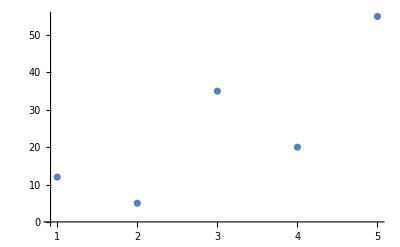

```mathematica
xcoor=Table[i,{i,1,5}];
ycoor={12,5,35,20,55};
Coordinates=Thread[{xcoor,ycoor}];
ListPlot[Coordinates]
```

```mathematica
7
```

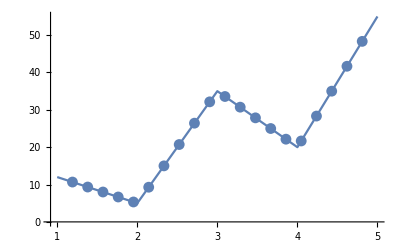

```mathematica
ListLinePlot[Coordinates,Mesh->20]
```

```mathematica
8
```

```mathematica
ListLinePlot[{Table[Cos[i ],{i,0,2π,0.2}],Table[Sin[i],{i,0,2π,0.2}]},PlotMarkers->{"⌘","▼"},PlotStyle->{Green,Black}]
```

-Graphics-

```mathematica
9
```

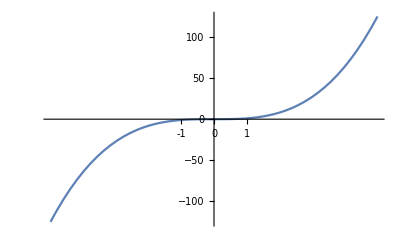

```mathematica
Plot[x^3,{x,-5,5},Ticks->{{-1,0,1}, Automatic}]
```

```mathematica
10
```

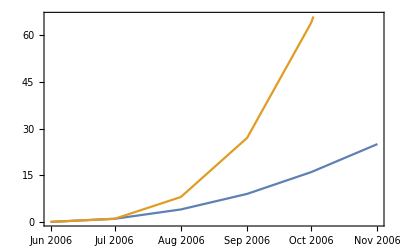

```mathematica
data1=Table[Power[i,2],{i,0,5}];
data2=Table[Power[i,3],{i,0,5}];
DateListPlot[{data1,data2},{2006,06}]
```

### Plotting Defined Functions

```mathematica
11
```

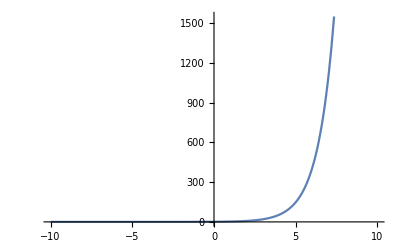

```mathematica
F[x_]:=Exp[x];
Plot[F[x],{x,-10,10}]
```

```mathematica
12
```

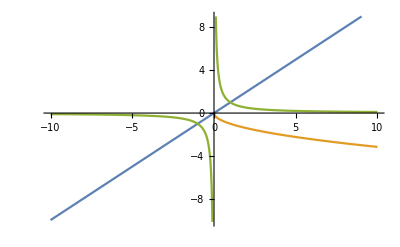

```mathematica
X[x_]:=x;Y[y_]:=-Sqrt[y];Z[z_]:=1/z;
Plot[{X[x],Y[x],Z[x]},{x,-10,10}]
```

### Adding text to charts

```mathematica
13
```

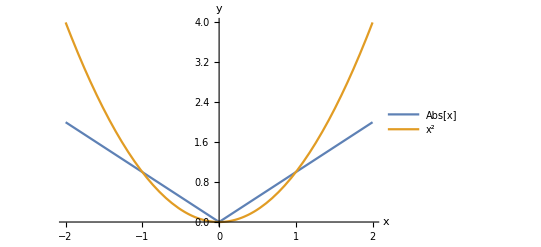

```mathematica
Plot[{Abs[x],x^2},{x,-2,2},AxesLabel->{"x","y"},PlotLegends->"Expressions"]
```

```mathematica
14
```


-Graphics-f(x) = x^2

```mathematica
Labeled[Plot[x^2,{x,-2,2}],"f(x) = x^2",Left]
```

```mathematica
15
```

```mathematica
Tooltip[{Plot[x^2,{x,-2,2}]}]
```

{-Graphics-}

```mathematica
16
```

```mathematica
Plot[Tooltip[x^2],{x,-2,2}]
```

-Graphics-

```mathematica
17
```

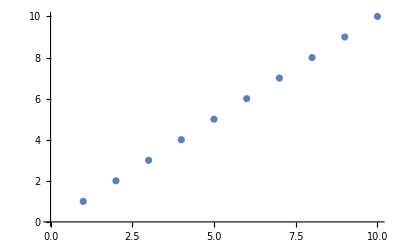

```mathematica
ListPlot[Tooltip[Range[10],TooltipStyle -> {Bold,Red,Background->LightBlue}]]
```

### Frame and Grids

```mathematica
18
```

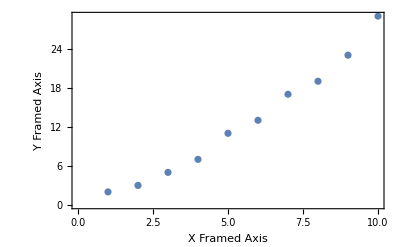

```mathematica
ListPlot[Table[Prime[i],{i,1,10}],Frame->True,FrameLabel->{"X Framed Axis ","Y Framed Axis"}]
```

```mathematica
19
```

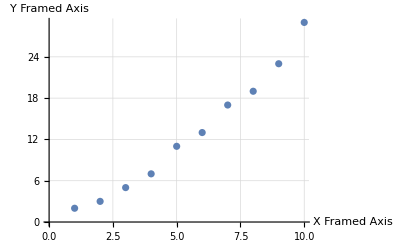

```mathematica
ListPlot[Table[Prime[i],{i,1,10}],GridLines->Automatic,AxesLabel->{"X Framed Axis ","Y Framed Axis"}]
```

```mathematica
20
```

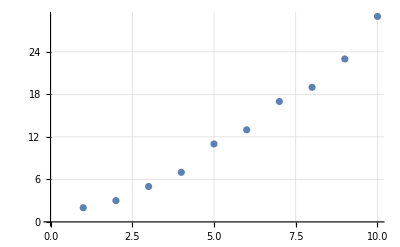

```mathematica
ListPlot[Table[Prime[i],{i,1,10}],GridLines->Automatic,GridLinesStyle->Directive[Thickness[0.0002],LightRed]]
```

### Filled Plots

```mathematica
21
```

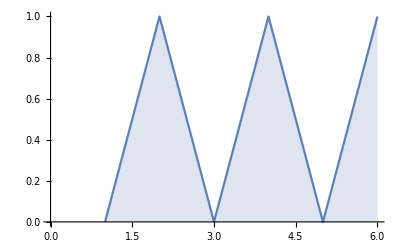

```mathematica
ListLinePlot[Table[Mod[i,2],{i,0,5}],Filling->Axis](* Filling-> Top or Bottom*)
```

```mathematica
22
```

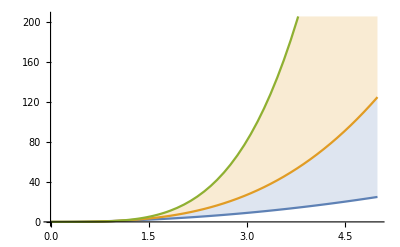

```mathematica
Plot[{x^2,x^3,x^4},{x,0,5},Filling->{1->{2},2->{3}}]
```

### Combining plots

```mathematica
23
```

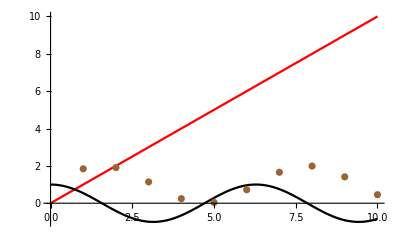

```mathematica
Plot1=Plot[x,{x,0,10},PlotStyle->Red];Plot2=Plot[Cos[x],{x,0,10},PlotStyle->Black];Plot3=ListPlot[Table[Sin[i]+1,{i,1,10}],PlotStyle->Brown];
Show[Plot1,Plot2,Plot3,PlotRange->Automatic]
```

```mathematica
24
```

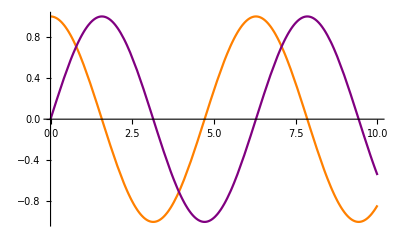

```mathematica
Show[Plot[Cos[x],{x,0,10},PlotStyle->Orange],Plot[Sin[x],{x,0,10},PlotStyle->Purple],PlotRange->Automatic]
```

```mathematica
25
```

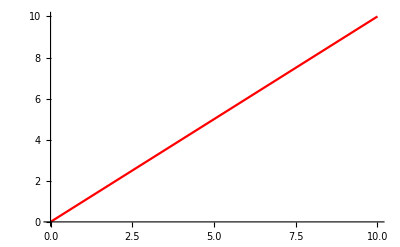
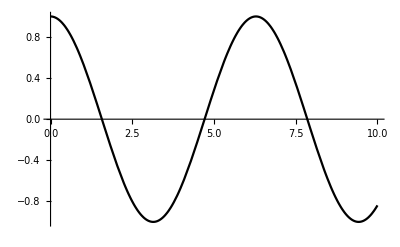
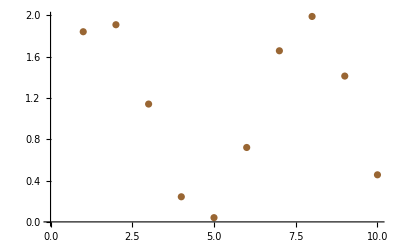

```mathematica
{Plot1,Plot2,Plot3}
```

```mathematica
26
```

```mathematica
Row[{Plot1,Plot2,Plot3}]
```

-Graphics--Graphics--Graphics-

```mathematica
27
```

```mathematica
Row[{Plot1,Plot2,Plot3},"**--**"]
```

**--****--**-Graphics--Graphics--Graphics-

```mathematica
28
```

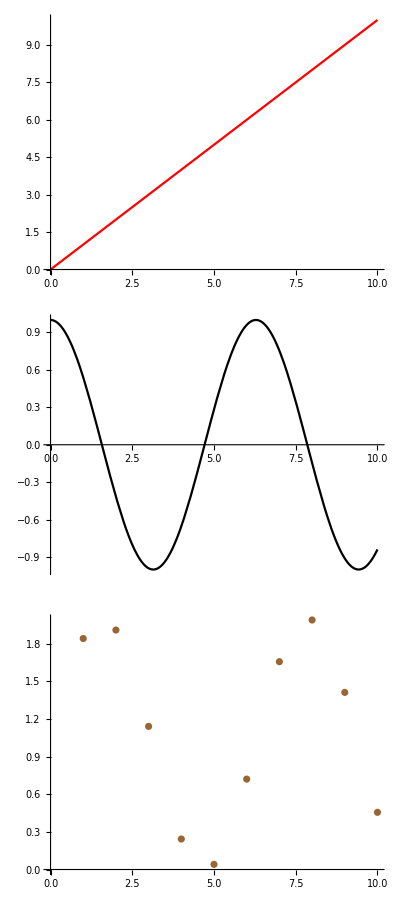

```mathematica
Column[{Plot1,Plot2,Plot3}]
```

```mathematica
29
```

```mathematica
{Column[{Plot1,Plot2,Plot3},Frame->True],Row[{Plot1,Plot2,Plot3},Frame->True,FrameMargins->Medium]}
```

{-Graphics-,-Graphics--Graphics--Graphics-}

```mathematica
30
```

```mathematica
Column[{Plot1,Plot2,Plot3},Frame->True,Background->LightCyan, FrameStyle->Directive[Black,Dashed],Dividers->All]
```

-Graphics-

```mathematica
31
```

```mathematica
Table[Row[{Plot1,Plot2,Plot3},Frame->True,FrameStyle->h],{h,{Thick,Dashed,Dotted}}]
```

{-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-}

```mathematica
32
```

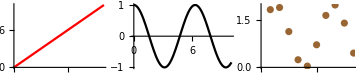

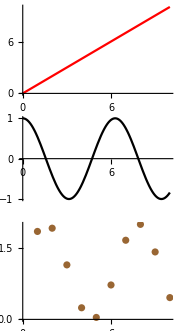

```mathematica
GraphicsRow[{Plot1,Plot2,Plot3},ImageSize->Medium]
GraphicsColumn[{Plot1,Plot2,Plot3},ImageSize->Small]
```

```mathematica
33
```

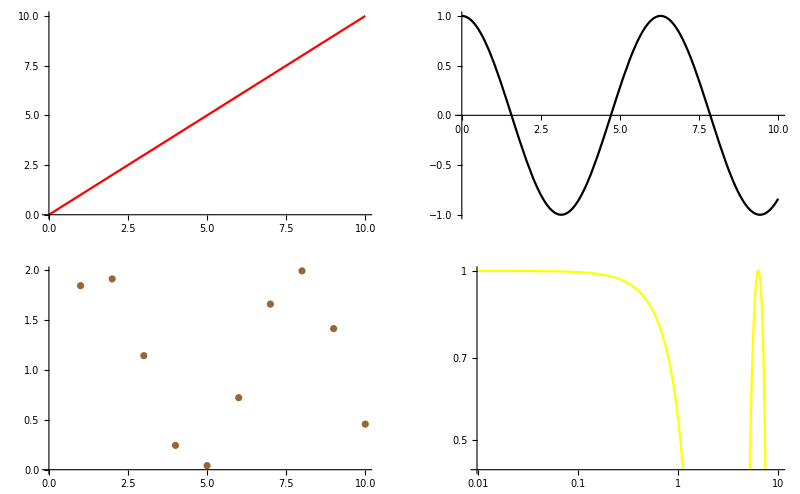

```mathematica
Plot4=LogLogPlot[Cos[x],{x,0,10},PlotStyle->Yellow];
GraphicsGrid[{{Plot1, Plot2}, 
 {Plot3,Plot4}},Frame->All, FrameStyle->Purple,Background->LightCyan]
```

```mathematica
34
```

```mathematica
NewPlot1=Plot[x,{x,0,10},PlotStyle->{Purple,Thick},PlotLabel->"X"];
NewPlot2=Plot[Cos[x],{x,0,10},GridLines->{{-1,0,1}, {-1,0,1}},GridLinesStyle->Directive[Dotted, Blue],PlotLabel->"Cos[x]",ColorFunction->"Rainbow"];
NewPlot3=ListPlot[Table[Sin[i]+1,{i,1,10}],Frame->True,FrameLabel->{Style["X",Bold],Style["Y",Bold]},PlotStyle->Red,PlotMarkers->"X",PlotLabel->"2D Scatter Plot"];
NewPlot4=LogLogPlot[Cos[x],{x,0,9},Filling->Axis,ColorFunction->"BlueGreenYellow",PlotLabel->"Log Log Plot",PlotRange->{0,1}];
```

```mathematica
35
```

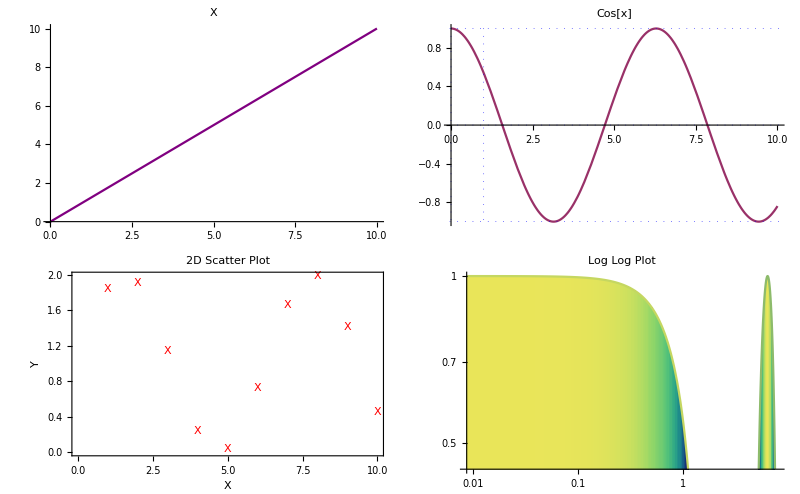
-Graphics-Multiple Plots Box

```mathematica
Labeled[GraphicsGrid[{{NewPlot1,NewPlot2},{NewPlot3,NewPlot4}},Frame->All,Background->White,Spacings->1],Style["Multiple Plots Box",20,Italic],Top,Frame->True,Background->LightYellow]
```

```mathematica
36
```

```mathematica
ColorData["BrownCyanTones"]
```

ColorDataFunction[…]

```mathematica
37
```

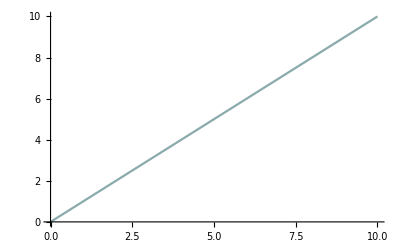

```mathematica
Plot[x,{x,0,10},ColorFunction->ColorData["BrownCyanTones"]]
```

### 3D plots

```mathematica
38
```

```mathematica
Plot3D[Sinc[x*8+y^2],{x,-1,2},{y,-1,3},ImageSize->Medium,PlotPoints->20]
```

-Graphics3D-

```mathematica
39
```

```mathematica
Plot3D[Sin[4(x^2+y^2)]/0.5,{x,-0.8,0.8},{y,-0.8,0.8},AxesLabel->{"X axis","Y axis","Z axis"},ColorFunction->"Rainbow",FaceGrids->All]
```

-Graphics3D-

```mathematica
40
```

```mathematica
Plot3D[Sin[0.9(x^2+y^2)]/0.5,{x,-1,1},{y,-1,1},AxesLabel->{"X axis","Y axis","Z axis"},FaceGrids->All,ColorFunction->Hue,PlotLabel->"My 3D Plot",Background->LightYellow,ViewAngle->Pi/7]
```

-Graphics3D-

```mathematica
41
```

```mathematica
Plot3D[Sin[0.9(x^2+y^3)]/0.5,{x,-1,1},{y,-1,1},FaceGrids->None,ColorFunction->(Hue[0.5,1,0.6,0.5]&),PlotLabel->Style["My 3D Plot",Italic,"Arial"],Background->Black]
```

-Graphics3D-

```mathematica
42
```

```mathematica
Row[
{
ListPlot3D[Table[RandomReal[1,5],{i,5}],ColorFunction->"SunsetColors",Ticks->None,PlotLegends->BarLegend[Automatic,LegendMarkerSize->90],ImageSize->Small,PlotLabel->"ListPlot3D",Filling->Bottom,BoxRatios->Automatic],ListPointPlot3D[Table[RandomReal[1,5],{i,5}],ColorFunction->"Rainbow",PlotLegends->BarLegend[Automatic,LegendMarkerSize->90],ImageSize->Small,PlotLabel->"ListPointPlot3D",Filling->Bottom,BoxStyle->Thick,BoxRatios->{1, 1, 1}]
},Background->Lighter[Gray, 0.80],Frame->True]
```

-Graphics3D--Graphics3D-

### Contour Plots

```mathematica
43
```

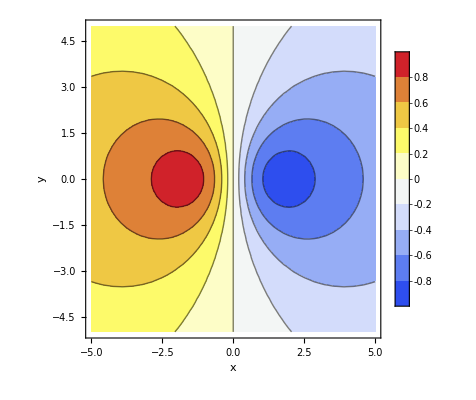

```mathematica
ContourPlot[(-π*x)/((x^2+y^2)+3),{x,-5,5},{y,-5,5},ColorFunction->"Temperature",PlotLegends->Automatic,FrameLabel->{x,y}]
```

```mathematica
44
```

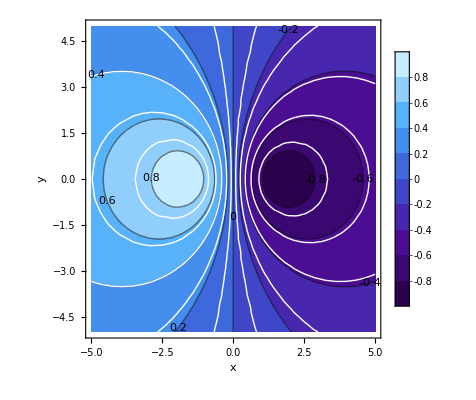

```mathematica
ContourPlot[(-π*x)/((x^2+y^2)+3),{x,-5,5},{y,-5,5},ColorFunction->"DeepSeaColors",PlotLegends->Automatic,FrameLabel->{x,y},ContourLabels->True,Mesh->{10,10},MeshStyle->{White}, MeshFunctions->{#3&}]
```

```mathematica
45
```

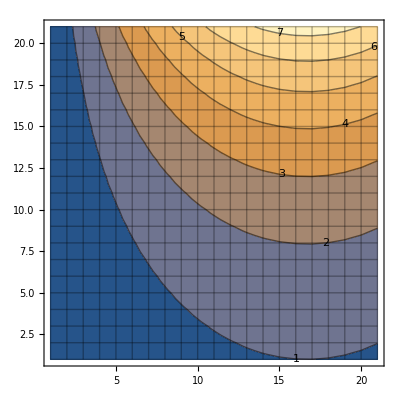

```mathematica
ListContourPlot[Table[Exp[x]*Sin[y],{x,0,2,.1},{y,0,2,.1}],ContourLines->True,Mesh->Full,ContourLabels->True]
```

```mathematica
46
```

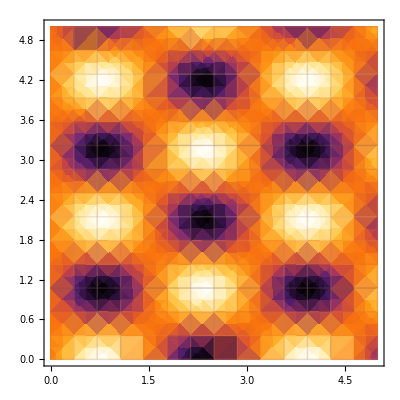

```mathematica
DensityPlot[(Sin[2x]*Cos[3y])/5,{x,0,5},{y,0,5},ColorFunction->"SunsetColors",Mesh->Full]
```

```mathematica
47
```

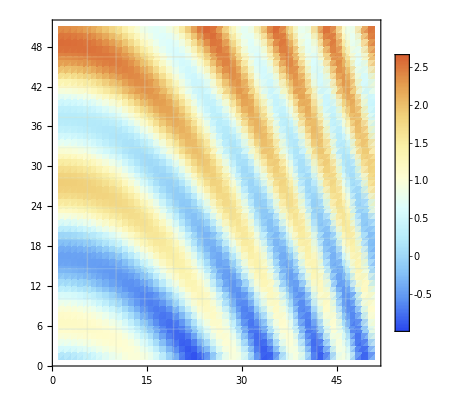

```mathematica
ListDensityPlot[Table[x/3+Sin[3x+y^2],{x,0,5,0.1},{y,0,5,0.1}],ColorFunction->"LightTemperatureMap",Mesh->10,PlotLegends->Placed[Automatic,Left]]
```

```mathematica
48
```

```mathematica
Show[Plot3D[(Sin[2x]*Cos[2y])/4,{x,0,2},{y,0,2},PlotStyle->Directive[Opacity[1]],AxesLabel->{"X axis","Y axis","Z axis"},ColorFunction->"Rainbow",PlotTheme->"Marketing"],SliceContourPlot3D[(Sin[2x]*Cos[2y])/4,{z==-0.15,z==0.15},{x,0,2},{y,0,2},{z,-1,1},ColorFunction->"Rainbow",Boxed->False],ViewPoint->{1,-1,1}]
```

-Graphics3D-

### Plot Themes

```mathematica
49
```

```mathematica
Data=Flatten[Table[{x,y,Sin[10(x^2+y^2)]/10},{x,-2,2,0.2},{y,-2,2,0.2}],1];ListPointPlot3D[Data,ColorFunction->"LightTemperatureMap",PlotTheme->"Detailed",ViewPoint->{0,-2,0},ImageSize->250,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->90],Left],ImageSize->20]
```

-Graphics3D-

```mathematica
50
```

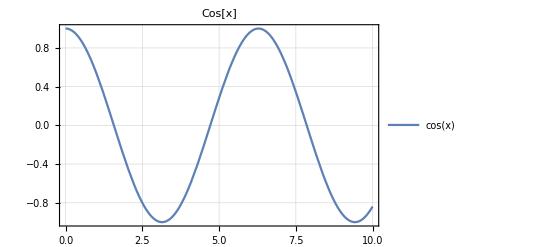

```mathematica
Plot[Cos[x],{x,0,10},PlotLabel->"Cos[x]",PlotTheme->"Detailed"]
```

```mathematica
51
```

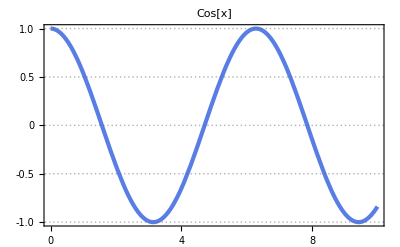
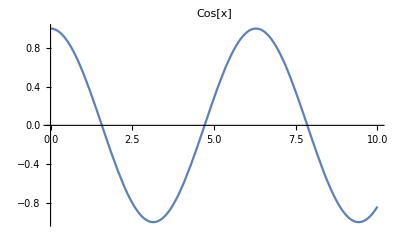

```mathematica
Table[Plot[Cos[x],{x,0,10},PlotLabel->"Cos[x]",PlotTheme->Pl],{Pl,{"Business","Minimal"}}]
```

```mathematica
52
```

```mathematica
ListPointPlot3D[Data,ColorFunction->"LightTemperatureMap",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->90],Left],PlotTheme->"Scientific",ViewProjection->"Orthographic"]
```

-Graphics3D-

```mathematica
53
```

```mathematica
ListPointPlot3D[Data,ColorFunction->"LightTemperatureMap",PlotTheme->"Scientific",ViewPoint->{0,0,-2},ImageSize->Medium]
```

-Graphics3D-